# Podatki o kriminalu policijske uprave Atlanta leta 2016

## Analiza podatkov o kriminalu policijske uprave Atlanta iz leta 2016 glede na različne dejavnike .

## Pridobivanje podatkov

Podatke sem pridobila iz podatkovne baze Wolfram data repository .

```mathematica
podatki  = ResourceData["Atlanta Police Department Crime Data (2009-2017)"]
```

Dataset[<>]

Zaradi velike količine pridobljenih podatkov, sem se odločila za analizo podatkov le enega leta . Iz cele tabele sem izbrala le relevantne podatke .

```mathematica
mojatab = podatki[0;;29112]
```

Dataset[<>]

## Analiza podatkov o zločinih glede na število žrtev

Analizirala ter narisala bom nekaj grafov zločinov glede na število žrtev (oškodovancev).
V seznamu zlocini so zbrani vsi zločini, ki so se zgodili leta 2016 v Atlanti. Podatki so prikazani tudi s tortnim diagramom in stolpičnim diagramom.

```mathematica
zlocini = mojatab[All, "UCGroup"]
```

Dataset[<>]

Funkcija SteviloZlocinov prešteje koliko je bilo posameznih zlocinov,  SeznamPoZlocinih pa nam nato podatke predstavi v obliki tabele.

```mathematica
SteviloZlocinov[zlocin_] := {zlocin, Count[zlocini, zlocin]}

SeznamPoZlocinih = SteviloZlocinov /@ (zlocini//DeleteDuplicates)
```

Te podatke lahko sedaj predstavimo s tortnim diagramom.

```mathematica
PieChart3D[
Normal[SeznamPoZlocinih[All, 2]],
ImageSize->{400, 400},
ChartLegends->Normal[SeznamPoZlocinih[All, 1]],
ChartStyle->{Green, Pink, Red, Blue, Yellow, Purple, Orange},
PlotLabel->"Prikaz števila različnih zločinov"
]
```

-Graphics3D-

Izračun števila vseh žrtev zločinov .

```mathematica
zrtve = Total[mojatab[All, "NumVictims"]]
```

33867

SteviloZrtevPoZlocinih nam proda število žrtev pri vsakem zločinu .

```mathematica
SteviloZrtev[zlocin_]:= {zlocin,Total[Select[mojatab, #["UCGroup"] == zlocin&][All, "NumVictims"]]} 

SteviloZrtevPoZlocinih = SteviloZrtev/@(zlocini//DeleteDuplicates)
```

SeznamZrtev in SeznamZlocinov nam zgornjo tabelo preoblikujeta v seznama, s pomočjo katerih lahko število žrtev prikažemo s stolpičnim diagramom.

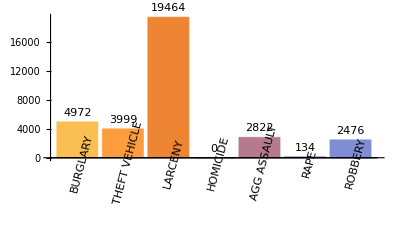

```mathematica
SeznamZrtev = Normal[SteviloZrtevPoZlocinih[[All, 2]]];
SeznamZlocinov = Normal[SteviloZrtevPoZlocinih[[All, 1]]];

BarChart[{SeznamZrtev},
ChartLabels->Placed[SeznamZlocinov,Below,Rotate[#,Pi/2.4]&] ,
LabelingFunction->Above]
```

## Analiza podatkov glede na čas

Analizirala bom zločine v Atlanti glede na mesec, v katerem so se zgodili.

```mathematica
SeznamDatumov = mojatab[All, "ReportDate"]
```

Dataset[<>]

```mathematica
SeznamMesecev = DateObject[#, "Month"]& /@ SeznamDatumov
```

Dataset[<>]

```mathematica
Stevilo[mesec_]:= {mesec, Count[SeznamMesecev, mesec]}
SteviloPoMesecih = Stevilo /@ (SeznamMesecev//DeleteDuplicates)
```

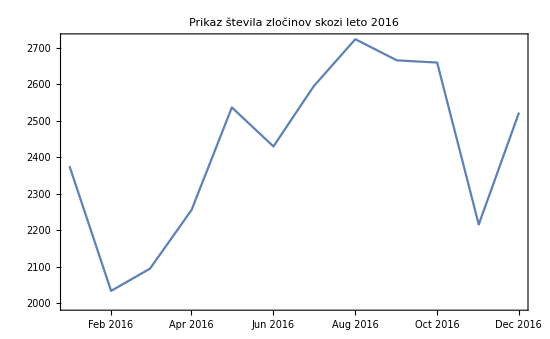

```mathematica
DateListPlot[SteviloPoMesecih, ImageSize->{550,500}, PlotLabel->"Prikaz števila zločinov skozi leto 2016"]
```

Iz grafa se da razbrati, da je bilo največ zločinov v mesecu avgustu, najmanj pa februarja. Vidi se tudi, da je število zločinov najvišje v toplejših mesecih (maj - oktober).
Naredila sem še nadaljno analizo tatvine (larceny), katerih je bilo leta 2016 skoraj 17.000.

### TATVINA:

```mathematica
tatvina = Select[mojatab, #["UCGroup"] == "LARCENY"&];
datumiT = tatvina[All, "ReportDate"];
seznamT = DateObject[#, "Month"]& /@ datumiT ;
stevilo[mesec_]:= {mesec, Count[seznamT, mesec]}
steviloPoMesecih = stevilo /@ (seznamT//DeleteDuplicates)
```

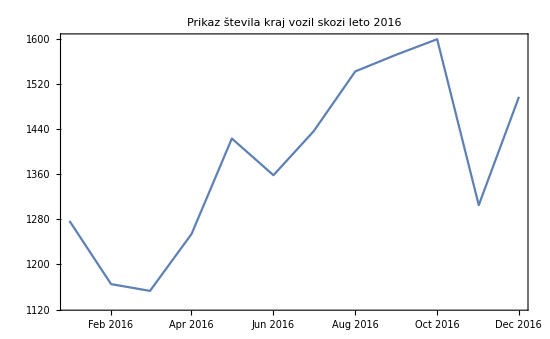

```mathematica
DateListPlot[steviloPoMesecih, ImageSize->{550,500}, PlotLabel->"Prikaz števila kraj vozil skozi leto 2016"]
```

## Analiza podatkov glede na lokacijo

Analizirala bom v katerih okoliših so se zgodili zločini.

```mathematica
SeznamKrajev = mojatab[All, "Neighborhood"]
```

Dataset[<>]

```mathematica
SteviloKrajev[kraj_]:= {kraj, Count[SeznamKrajev, kraj]}
SeznamPoKrajih = 
SteviloKrajev /@ (SeznamKrajev//DeleteDuplicates)
```

Največje število in kraj :

```mathematica
prvo = Select[SeznamPoKrajih,
#[[2]] == Max[SeznamPoKrajih[All,2]]&]
```

Najmanjše število in kraj :

```mathematica
zadnje = Select[SeznamPoKrajih,
#[[2]] == Min[SeznamPoKrajih[All,2]]&]
```

Največ zločinov se po podanih podatkih zgodi v Downtownu, ali središče Atlante, najmanj pa se jih zgodi v manjših naseljih v okolici. Spodaj sem prikazala, kateri zločini so bili v tem delu Atlante najbolj pogosti ter jih predstavila s stolpičnim diagramom.

```mathematica
Downtown = Select[mojatab, #["Neighborhood"] == "Downtown"&];

zlociniDowntown = Downtown[All, "UCGroup"];

SteviloZlocinov[zlocin_] := {zlocin, Count[zlociniDowntown, zlocin]}

SeznamPoZlocinih = SteviloZlocinov /@ (zlociniDowntown//DeleteDuplicates)
```

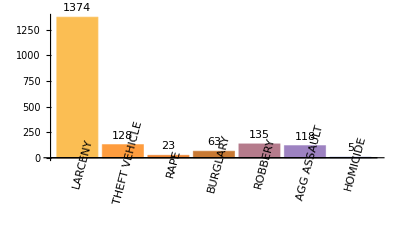

```mathematica
DowntownZrtve= Normal[SeznamPoZlocinih[[All, 2]]];

DowntownZlocinov = Normal[SeznamPoZlocinih[[All, 1]]];

BarChart[{DowntownZrtve},
ChartLabels->Placed[DowntownZlocinov,Below,Rotate[#,Pi/2.4]&] ,
LabelingFunction->Above]
```

Funkcija Downtown nam zoža seznam podatkov le na zločin, ki so se zgodili v kraju Downtown. Nato pa s funkcijo SeznamPoZlocinih naredimo tabelo.